```mathematica
Needs["ErrorBarPlots`"]
LinReg[daten_]:=Module[{x,y,Δy,S,Δa0,Δb0,a0,b0,n,squadrat,ymitt,Rquadrat,Χquadrat},
n=Length[daten];
x=daten[[All,1]];
y=daten[[All,2]];
Δy=daten[[All,3]];

Χquadrat=∑_(i=1)^n (1/Δy⟦i⟧*(y⟦i⟧-a0-(b0*x⟦i⟧)))^2;

squadrat=Χquadrat/(n-2);
ymitt=(∑_(i=1)^n y⟦i⟧/(Δy⟦i⟧)^2)/(∑_(i=1)^n 1/(Δy⟦i⟧)^2);
Rquadrat=1-(∑_(i=1)^n (y⟦i⟧-a0-b0*x⟦i⟧)^2/(Δy⟦i⟧)^2)/(∑_(i=1)^n (y⟦i⟧-ymitt)^2/(Δy⟦i⟧)^2);
S=∑_(i=1)^n 1/(Δy⟦i⟧)^2*∑_(i=1)^n (x⟦i⟧)^2/(Δy⟦i⟧)^2-(∑_(i=1)^n x⟦i⟧/(Δy⟦i⟧)^2)^2;
a0=1/S*(∑_(i=1)^n (x⟦i⟧)^2/(Δy⟦i⟧)^2*∑_(i=1)^n y⟦i⟧/(Δy⟦i⟧)^2-∑_(i=1)^n x⟦i⟧/(Δy⟦i⟧)^2*∑_(i=1)^n (x⟦i⟧*y⟦i⟧)/(Δy⟦i⟧)^2);
b0=1/S*(∑_(i=1)^n 1/(Δy⟦i⟧)^2*∑_(i=1)^n (y⟦i⟧*x⟦i⟧)/(Δy⟦i⟧)^2-∑_(i=1)^n x⟦i⟧/(Δy⟦i⟧)^2*∑_(i=1)^n y⟦i⟧/(Δy⟦i⟧)^2);
Δa0=Sqrt[1/S*∑_(i=1)^n (x⟦i⟧)^2/(Δy⟦i⟧)^2];
Δb0=Sqrt[1/S*∑_(i=1)^n 1/(Δy⟦i⟧)^2];
Print["Berechnung der Fehler aus den Eingangsfehlern"];
Print[TableForm[{{"","Wert","Fehler"},{"Steigung b",b0,Δb0},{"Achsenabschnitt a",a0,Δa0},{"R^2",Rquadrat},{"S^2",squadrat},{"n",n},{"Χquadrat/(n - 2)",Χquadrat/(n-2)}}]];
{b->b0,Δb->Δb0,a->a0,Δa->Δa0}]
```

```mathematica
aufspaltung=ReadList["C:\\Users\\Vincent\\Documents\\GitHub\\Zeeman-Effekt\\Vincent\\wellenzahl_aufspaltung.txt",{Real,Real,Real}]
```

{{0.48,0.86,1.4},{0.57,1.29,1.5},{0.66,1.63,1.5},{0.75,1.93,1.6},{0.82,2.12,1.6},{0.89,2.25,1.6}}

```mathematica
regerg=LinReg[aufspaltung]
```

Berechnung der Fehler aus den Eingangsfehlern

| Wert | Fehler
Steigung b | 3.43184 | 4.35386
Achsenabschnitt a | -0.706665 | 3.03263
R^2 | 0.981586 | 
S^2 | 0.0029138 | 
n | 6 | 
Χquadrat/(n - 2) | 0.0029138 |

{b→3.43184,Δb→4.35386,a→-0.706665,Δa→3.03263}

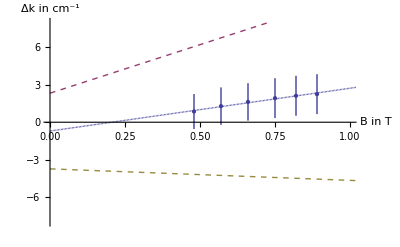

```mathematica
Show[Plot[Evaluate[{b*t+a,(b+Δb)*t+a+Δa,(b-Δb)*t+a-Δa}/.regerg],{t,0,2},AxesStyle->Directive[25],PlotRange->{{0,1},{-8,8}},AxesLabel->{Style["B in T",FontSize->33], Style["Δk in cm^-1",FontSize->33]},PlotStyle->{Dashing[{.0}],Dashing[{0.01}],Dashing[{.01}]}],ErrorListPlot[aufspaltung]]
```

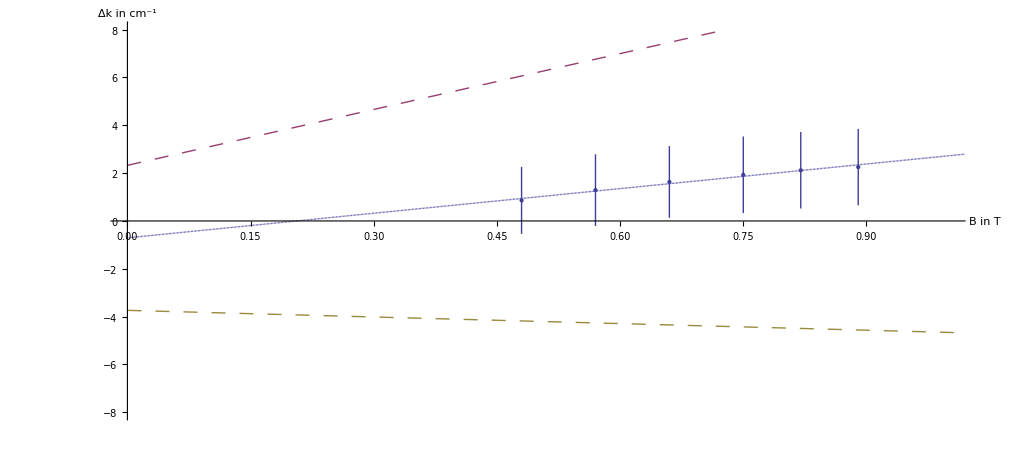

```mathematica
Show[%86,ImageSize->{1009,460},AspectRatio->Full]
```

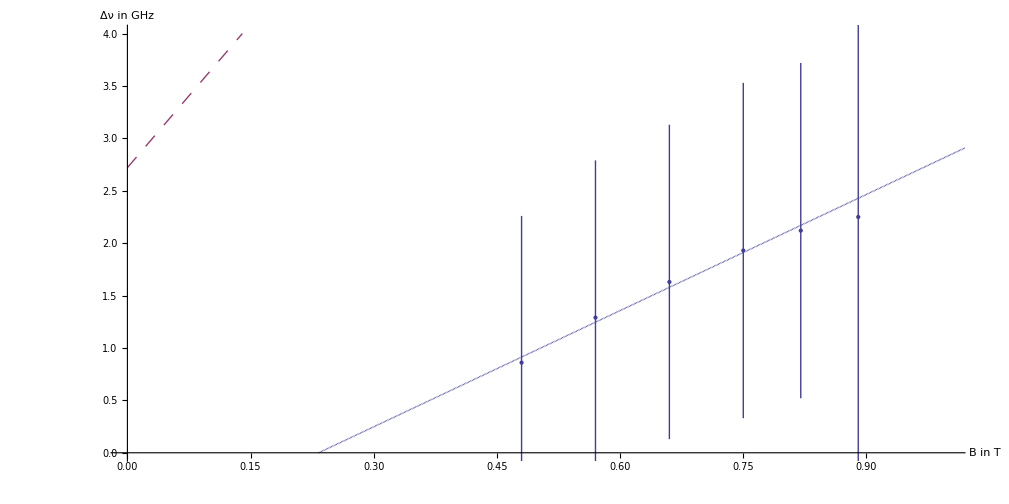

```mathematica
Show[%15,ImageSize->{1009,504},AspectRatio->Full]
```

```mathematica
Show[%12,ImageSize->{1006,545},AspectRatio->Full]
```

Show::gtype: Symbol is not a type of graphics.

Show[Null,ImageSize→{1006,545},AspectRatio→Full]

```mathematica
Show[%215,ImageSize->{1003,532},AspectRatio->Full]
```

Show::gtype: Out is not a type of graphics.

Show[%215,ImageSize→{1003,532},AspectRatio→Full]